# Visualisation of Multiplex ABM

### Curate the data

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/Network_Modelling/ABM/Multi_layer"];
```

```mathematica
(* Import the 'physical' node data, sigma=0 and sigma=1 *)
rawp0=Import["Build/Products/Debug/node_data_phys.txt","Data"];
rawp1=Import["Build/Products/Debug/node_data_phys2.txt","Data"];
```

```mathematica
(* Import the 'virtual' node data *)
rawv0=Import["Build/Products/Debug/node_data_virt.txt","Data"];
rawv1=Import["Build/Products/Debug/node_data_virt2.txt","Data"];
```

```mathematica
(* Import data on infectant count *)
rawinf0=Import["Build/Products/Debug/ts.txt","Data"];
inftotal0=rawinf0[[;;,2]];

rawinf1=Import["Build/Products/Debug/ts3.txt","Data"];
inftotal1=rawinf1[[;;,2]];
```

```mathematica
(* Curate the data into manageable form *)
nodephys0=Partition[rawp0,50];
nodevirt0=Partition[rawv0,50];
nodephys1=Partition[rawp1,50];
nodevirt1=Partition[rawv1,50];
```

### Make the frames

```mathematica
(* Plot the graphs *)
graph0=ListPlot[inftotal0, AxesLabel->{"time","# infected"}, AspectRatio->0.5,PlotMarkers->{Automatic,3},PlotRange->All];
graph1=ListPlot[inftotal1, AxesLabel->{"time","# infected"}, AspectRatio->0.5,PlotMarkers->{Automatic,3},PlotRange->All];
```

```mathematica
(* Function that determines the colour of the node (i,j) *)

colour["s"]=GrayLevel[0.8];
colour["i"]=Red;
colour["u"]=GrayLevel[0.8];
colour["a"]=Blue;
```

```mathematica
(* Lattice plots *)

latticephys0[k_]:=Graphics[Table[
{PointSize[0.012],colour[nodephys0[[k,i,j]]],Point[{i,j}]},{i,50},{j,50}
],ImageSize->400]

latticevirt0[k_]:=Graphics[Table[
{PointSize[0.012],colour[nodevirt0[[k,i,j]]],Point[{i,j}]},{i,50},{j,50}
],ImageSize->400]

latticephys1[k_]:=Graphics[Table[
{PointSize[0.012],colour[nodephys1[[k,i,j]]],Point[{i,j}]},{i,50},{j,50}
],ImageSize->400]

latticevirt1[k_]:=Graphics[Table[
{PointSize[0.012],colour[nodevirt1[[k,i,j]]],Point[{i,j}]},{i,50},{j,50}
],ImageSize->400]
```

```mathematica
(* Make a legend *)

legend1 = PointLegend[{Directive[GrayLevel[0.8], AbsolutePointSize[20]], Directive[Red, AbsolutePointSize[20]]}, {"Susceptible", "Infected"}, LegendLabel->Text[Style["Physical Layer",FontSize->16,Italic]],LegendMarkerSize->30];

legend2 = PointLegend[{ Directive[GrayLevel[0.8], AbsolutePointSize[20]], Directive[Blue, AbsolutePointSize[20]]}, {"Unaware", "Aware"}, LegendLabel->Text[Style["Virtual Layer",FontSize->16,Italic]],LegendMarkerSize->30];
```

```mathematica
legend=Grid[{{legend1,legend2}}]
```

|

```mathematica
title="\nVisualisation for a Multiplex ABM with SIS and UAU Dynamics";
parameters0="Parameters: σ=0, γ=0, β=1, μ=0.1, λ=0.1, δ=0";
parameters1="Parameters: σ=1, γ=0, β=1, μ=0.1, λ=0.1, δ=0";
```

```mathematica
(* Frame fuction, note there are 400 frames altogether *)
frame0[k_]:=Grid[{
{Text[Style[title,FontSize->20]],SpanFromLeft},
{Text[Style[parameters0,FontSize->14,Italic]],SpanFromLeft},
{Show[graph0,Graphics[Line[{{k,0},{k,1600}}]],ImageSize->400],legend},
{latticephys0[k],latticevirt0[k]}}
]

frame1[k_]:=Grid[{
{Text[Style[title,FontSize->20]],SpanFromLeft},
{Text[Style[parameters1,FontSize->14,Italic]],SpanFromLeft},
{Show[graph1,Graphics[Line[{{k,0},{k,1600}}]],ImageSize->400],legend},
{latticephys1[k],latticevirt1[k]}}
]
```

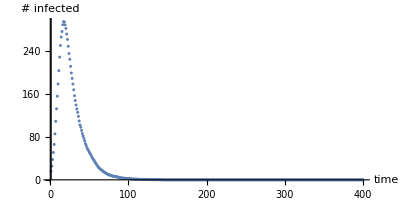
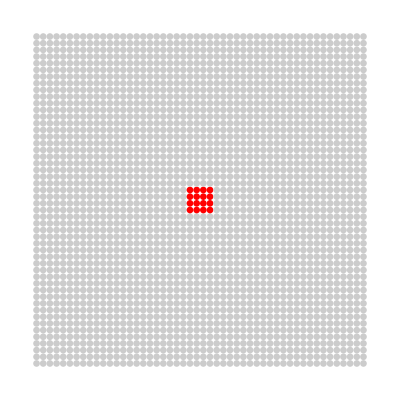
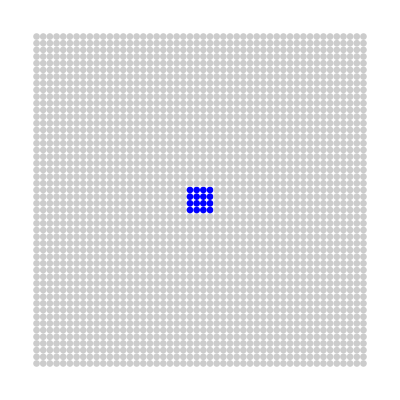
Visualisation for a Multiplex ABM with SIS and UAU Dynamics | 
Parameters: σ=1, γ=0, β=1, μ=0.1, λ=0.1, δ=0 | 
-Graphics- |  | 
-Graphics- | -Graphics-

```mathematica
frame1[1]
```

### Make the movie

```mathematica
frames0=Table[frame0[i],{i,1,100,2}];
```

```mathematica
Export["sim1_0.mov",frames0,"FrameRate"->8,ImageSize->900,Antialiasing->True,"VideoEncoding"->"Apple Intermediate Codec"];
```

```mathematica
frames1=Table[frame1[i],{i,1,100,2}];
```

```mathematica
Export["sim1_1.mov",frames1,"FrameRate"->8, ImageSize->900,Antialiasing->True,"VideoEncoding"->"Apple Intermediate Codec"];
```